Working in natural units.
Thermal baths are bosonic and Ohmic.

```mathematica
unitassum={ℏ->1,k->1};
NBEassum=Subscript[NBE, P_][ω_]-> 1/(ⅇ^((ℏ ω)/(k Subscript[T, P]))-1);
Jassum=Subscript[J, P_][ω_]->Subscript[κ, P] ω;

Tconv=1;
ωconv=(Tconv k)/ℏ/.unitassum;
tconv=ℏ/(Tconv k)/.unitassum;
Τconv=(Tconv k)/ℏ/.unitassum;
Econv=(Tconv k)^2/ℏ/.unitassum;
```

### Density matrix

```mathematica
ρMatrix[t]=Table[Subscript[ρ, {i,j}][t],{i,1,2},{j,1,2}];
MatrixForm[%]
```

(ρ_{1,1}[t] | ρ_{1,2}[t]
ρ_{2,1}[t] | ρ_{2,2}[t])

### System Hamiltonian

```mathematica
Hs = (ℏ ω)/2({{1, 0}, {0, -1}});
```

### Get projection matrices Π(ϵ)

```mathematica
πMatrix[1]=({{1, 0}, {0, 0}});
πMatrix[2]=({{0, 0}, {0, 1}});
```

### Get Lindblad operators A^P(ω)

Only a single Lindblad operator exists.

```mathematica
AMatrix[ω]=πMatrix[2].({{0, 1}, {1, 0}}).πMatrix[1];
%//MatrixForm
```

(0 | 0
1 | 0)

### Calculate Lindbladian terms

```mathematica
Subscript[LinMatrix, P_][ρ_]:=(Subscript[J, P][ω](1+Subscript[NBE, P][ω])(AMatrix[ω].ρ.AMatrix[ω]†-1/2(AMatrix[ω]†.AMatrix[ω].ρ+ρ.AMatrix[ω]†.AMatrix[ω]))+Subscript[J, P][ω]Subscript[NBE, P][ω](AMatrix[ω]†.ρ.AMatrix[ω]-1/2(AMatrix[ω].AMatrix[ω]†.ρ+ρ.AMatrix[ω].AMatrix[ω]†)))
```

```mathematica
Simplify[Subscript[LinMatrix, 1][ρMatrix[t]]]//MatrixForm
Simplify[Subscript[LinMatrix, 2][ρMatrix[t]]]//MatrixForm
```

(J_1[ω] (-((1+NBE_1[ω]) ρ_{1,1}[t])+NBE_1[ω] ρ_{2,2}[t]) | -1/2 J_1[ω] (1+2 NBE_1[ω]) ρ_{1,2}[t]
-1/2 J_1[ω] (1+2 NBE_1[ω]) ρ_{2,1}[t] | J_1[ω] ((1+NBE_1[ω]) ρ_{1,1}[t]-NBE_1[ω] ρ_{2,2}[t]))

(J_2[ω] (-((1+NBE_2[ω]) ρ_{1,1}[t])+NBE_2[ω] ρ_{2,2}[t]) | -1/2 J_2[ω] (1+2 NBE_2[ω]) ρ_{1,2}[t]
-1/2 J_2[ω] (1+2 NBE_2[ω]) ρ_{2,1}[t] | J_2[ω] ((1+NBE_2[ω]) ρ_{1,1}[t]-NBE_2[ω] ρ_{2,2}[t]))

### Master equation

∂_t ρ[t] = ℒ_1[ρ[t]]+ℒ_2[ρ[t]]

ℒ_P[ρ] = 𝒥_P[ω](1+n_P[ω])(A[ω].ρ.A[ω]† - 1/2{A[ω]†A[ω],ρ})+𝒥_P[ω]n_P[ω](A[ω]†.ρ.A[ω] - 1/2{A[ω]A[ω]†,ρ})

n_P[ω] = 1/(ⅇ^((ℏ ω)/(k T_P))-1)
J_P[ω] = κ_P ω

```mathematica
sol=Flatten[Solve[D[ρMatrix[t], t] == Subscript[LinMatrix, 1][ρMatrix[t]]+Subscript[LinMatrix, 2][ρMatrix[t]],Flatten[Table[Subscript[ρ, {i,j}]'[t],{i,1,2},{j,1,2}]]]//.Rule->Equal];

Flatten[Table[Subscript[J, P][ ω],{P,1,2}]];
Flatten[Table[Subscript[ρ, {i,j}][t],{i,1,2},{j,1,2}]];
sol=ApplySides[Collect[Expand[#],%%,Collect[#,%]&]&,sol]
```

{ρ_{1,1}'[t]==J_1[ω] ((-1-NBE_1[ω]) ρ_{1,1}[t]+NBE_1[ω] ρ_{2,2}[t])+J_2[ω] ((-1-NBE_2[ω]) ρ_{1,1}[t]+NBE_2[ω] ρ_{2,2}[t]),ρ_{1,2}'[t]==J_1[ω] (-1/2-NBE_1[ω]) ρ_{1,2}[t]+J_2[ω] (-1/2-NBE_2[ω]) ρ_{1,2}[t],ρ_{2,1}'[t]==J_1[ω] (-1/2-NBE_1[ω]) ρ_{2,1}[t]+J_2[ω] (-1/2-NBE_2[ω]) ρ_{2,1}[t],ρ_{2,2}'[t]==J_1[ω] ((1+NBE_1[ω]) ρ_{1,1}[t]-NBE_1[ω] ρ_{2,2}[t])+J_2[ω] ((1+NBE_2[ω]) ρ_{1,1}[t]-NBE_2[ω] ρ_{2,2}[t])}

### Energy flow inwards

Energy flow rates are given by

J_P[ρ] = Tr[ℒ_P[ρ].Hs]

```mathematica
Subscript[EngyFlowIn, P_][ρ_]:=Simplify[Tr[Subscript[LinMatrix, P][ρ].Hs]]
```

```mathematica
Subscript[EngyFlowIn, 1][ρMatrix[t]]
Subscript[EngyFlowIn, 2][ρMatrix[t]]
```

-ω ℏ J_1[ω] ((1+NBE_1[ω]) ρ_{1,1}[t]-NBE_1[ω] ρ_{2,2}[t])

-ω ℏ J_2[ω] ((1+NBE_2[ω]) ρ_{1,1}[t]-NBE_2[ω] ρ_{2,2}[t])

### Dynamics (time domain) of the device

Assumptions on the temperatures of the baths, TLS energy levels, and TLS interaction strengths,

```mathematica
Tassum={Subscript[T, 1]-> 0.2 Tconv,Subscript[T, 2]-> 0.02 Tconv,ω->1 ωconv,Subscript[κ, 1]-> 0.01,Subscript[κ, 2]->0.01 };
```

Numerical solution of the dynamics, with the initial condition that all density matrix elements except the first are zero.

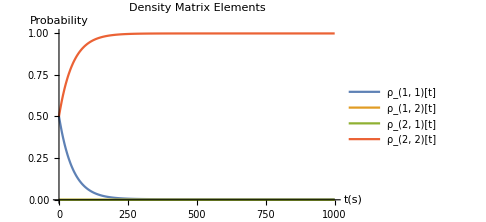

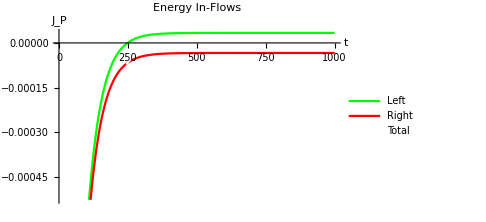

```mathematica
tmax=(1000/ω)//.Flatten[{unitassum,Tassum}];

dynamics=NDSolve[
Flatten[{sol//.Flatten[{Jassum,NBEassum,Tassum,unitassum}],Table[Subscript[ρ, {i,j}][0]==i,j 0.5,{i,1,2},{j,1,2}]}]
,Flatten[Table[Subscript[ρ, {i,j}],{i,1,2},{j,1,2}]],{t,0,tmax}
];

Flatten[{Table[Subscript[ρ, {i,j}][t],{i,1,2},{j,1,2}]}/.dynamics];
Plot[%,{t,0,tmax},PlotRange-> {0.,1},ImageSize->Medium,PlotLabel->  Style["Density Matrix Elements"],AxesLabel->{Style["t(s)"],Style["Probability"]}, 
PlotLegends->{
Style["ρ_(1, 1)[t]"],Style["ρ_(1, 2)[t]"],Style["ρ_(2, 1)[t]"],Style["ρ_(2, 2)[t]"]}]

Flatten[{Subscript[EngyFlowIn, 1][ρMatrix[t]],Subscript[EngyFlowIn, 2][ρMatrix[t]],Subscript[EngyFlowIn, 1][ρMatrix[t]]+Subscript[EngyFlowIn, 2][ρMatrix[t]]}//.Flatten[{Jassum,NBEassum,Tassum,unitassum}]/.dynamics];
Plot[%,{t,0,tmax},AxesLabel->{"t","J_P"},ImageSize->Medium,PlotLabel-> Style["Energy In-Flows"],PlotLegends->{"Left ","Right","Total"},PlotStyle->{Green,Red,{White,Dashed}}]
```

### Solve the master equation for a stationary state

```mathematica
ρMatrixStat=Table[Subscript[ρ, {i,j}],{i,1,2},{j,1,2}];
MatrixForm[%]
```

(ρ_{1,1} | ρ_{1,2}
ρ_{2,1} | ρ_{2,2})

```mathematica
solstat = Flatten[Solve[{({{0, 0}, {0, 0}})== Subscript[LinMatrix, 1][ρMatrixStat]+Subscript[LinMatrix, 2][ρMatrixStat],Subscript[ρ, {1,1}]+Subscript[ρ, {2,2}]==1},{Subscript[ρ, {1,1}],Subscript[ρ, {1,2}],Subscript[ρ, {2,1}],Subscript[ρ, {2,2}]}]];
statstate=Simplify[ρMatrixStat/.solstat];
MatrixForm[statstate]
```

((J_1[ω] NBE_1[ω]+J_2[ω] NBE_2[ω])/(J_1[ω] (1+2 NBE_1[ω])+J_2[ω] (1+2 NBE_2[ω])) | 0
0 | (J_1[ω] (1+NBE_1[ω])+J_2[ω] (1+NBE_2[ω]))/(J_1[ω] (1+2 NBE_1[ω])+J_2[ω] (1+2 NBE_2[ω])))

(0.00336897 | 0
0 | 0.996631)

### Energy flows at steady state

```mathematica
Simplify[Subscript[EngyFlowIn, 1][statstate]]
Simplify[Subscript[EngyFlowIn, 1][statstate]//.Flatten[{Jassum,NBEassum,unitassum,Subscript[T, 1]->TL,Subscript[T, 2]->TR,Subscript[κ, 1]->κL,Subscript[κ, 2]->κR}]]
```

(ω ℏ J_1[ω] J_2[ω] (NBE_1[ω]-NBE_2[ω]))/(J_1[ω] (1+2 NBE_1[ω])+J_2[ω] (1+2 NBE_2[ω]))

-((ⅇ^(ω/TL)-ⅇ^(ω/TR)) κL κR ω^2)/((1+ⅇ^(ω/TL)) (-1+ⅇ^(ω/TR)) κL+(-1+ⅇ^(ω/TL)) (1+ⅇ^(ω/TR)) κR)

At steady state, the rate of heat absorption from the left reservoir,

```mathematica
EnergyFlow[ω_,TL_,TR_,κL_,κR_]:=-((ⅇ^(ω/TL)-ⅇ^(ω/TR)) κL κR ω^2)/((1+ⅇ^(ω/TL)) (-1+ⅇ^(ω/TR)) κL+(-1+ⅇ^(ω/TL)) (1+ⅇ^(ω/TR)) κR)
```

### Test if the values match

```mathematica
statstate//.Flatten[{Jassum,Tassum,NBEassum,unitassum}]//MatrixForm
```

(0.00336897 | 0
0 | 0.996631)

```mathematica
EnergyFlow[ω,Subscript[T, 1],Subscript[T, 2],Subscript[κ, 1],Subscript[κ, 2]]/.{Tassum}
```

{0.0000336897}